```mathematica
Integrate[((a - x)^2 + b(y - x^2)^2),{x,xlower,xupper},{y,ylower, yupper}]
```

-a (xlower^2-xupper^2) (ylower-yupper)+1/5 b (xlower^5-xupper^5) (ylower-yupper)-1/3 (xlower^3-xupper^3) (ylower-yupper) (-1+b (ylower+yupper))+1/3 (xlower-xupper) (3 a^2 (ylower-yupper)+b (ylower^3-yupper^3))

```mathematica
1/(75.83333333333333-32.5 a+32.5 a^2+300.62500000000006 b) Integrate[((a - x)^2 + b(y - x^2)^2),{x,xlower,xupper},{y,ylower, yupper}]
```

(-a (xlower^2-xupper^2) (ylower-yupper)+1/5 b (xlower^5-xupper^5) (ylower-yupper)-1/3 (xlower^3-xupper^3) (ylower-yupper) (-1+b (ylower+yupper))+1/3 (xlower-xupper) (3 a^2 (ylower-yupper)+b (ylower^3-yupper^3)))/(75.8333-32.5 a+32.5 a^2+300.625 b)

```mathematica
fRosenbrockPDF[x_,y_,a_,b_,xlower_,xupper_,ylower_,yupper_]:=(-a (xlower^2-xupper^2) (ylower-yupper)+1/5 b (xlower^5-xupper^5) (ylower-yupper)-1/3 (xlower^3-xupper^3) (ylower-yupper) (-1+b (ylower+yupper))+1/3 (xlower-xupper) (3 a^2 (ylower-yupper)+b (ylower^3-yupper^3)))/(75.83333333333333-32.5 a+32.5 a^2+300.62500000000006 b)
```

```mathematica
NIntegrate[fRosenbrockPDF[x,y,1,100,-2,3,-1,6],{x,-2,3},{y,-1,6}]
```

39.3859

```mathematica
0.00003318033512138472 (-1. (-4.+x1^2) (0.5+y1)+20. (32.+x1^5) (0.5+y1)-0.3333333333333333 (8.+x1^3) (-0.5-1. y1+100 (-0.25+1. y1^2))+(2+x1) (0.5+y1+100 (0.041666666666666664+0.3333333333333333 y1^3)))
```

```mathematica
0.00003318033512138472 (-1. (-4.+x1^2) (0.5+y1)+20. (32.+x1^5) (0.5+y1)-0.3333333333333333 (8.+x1^3) (-0.5-1. y1+100 (-0.25+1. y1^2))+(2+x1) (0.5+y1+100 (0.041666666666666664+0.3333333333333333 y1^3)))/.{x1->3, y1->6}
```

1.

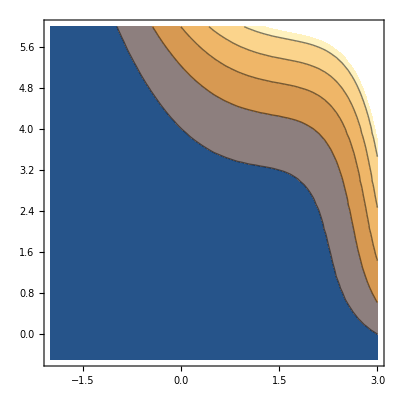

```mathematica
ContourPlot[0.00003318033512138472 (-1. (-4.+x1^2) (0.5+y1)+20. (32.+x1^5) (0.5+y1)-0.3333333333333333 (8.+x1^3) (-0.5-1. y1+100 (-0.25+1. y1^2))+(2+x1) (0.5+y1+100 (0.041666666666666664+0.3333333333333333 y1^3))),{x1,-2,3},{y1,-0.5,6}]
```

```mathematica
-1. a (-4.+x1^2) (0.5+y1)+0.2 b (32.+x1^5) (0.5+y1)-0.3333333333333333 (8.+x1^3) (-0.5-1. y1+b (-0.25+1. y1^2))+(2+x1) (a^2 (0.5+y1)+b (0.041666666666666664+0.3333333333333333 y1^3))
```

```mathematica
Integrate[((a - x)^2 + b(y - x^2)^2),{x,-2,3},{y,-0.5, 5}]/.{a->1, b->100}
```

22293.3

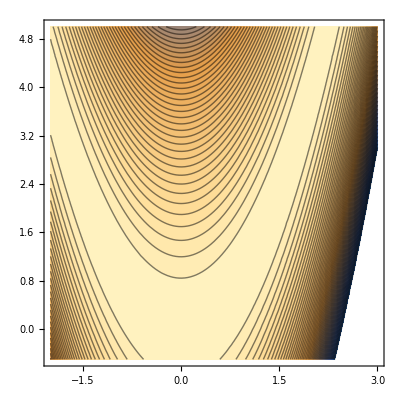

```mathematica
ContourPlot[-((a - x)^2 + b(y - x^2)^2)/.{a->1, b->100},{x,-2,3},{y,-0.5, 5},Contours->50]
```